{1,0.6,0.48,0.444,0.4332,0.42996,0.428988,0.428696,0.428609,0.428583,0.428575}

{1,0.6,0.48,0.444,0.4332,0.42996,0.428988,0.428696,0.428609,0.428583,0.428575}

{1,0.7,0.61,0.583,0.5749,0.57247,0.571741,0.571522,0.571457,0.571437,0.571431}

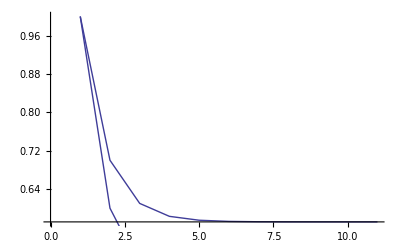

```mathematica
P[n_]:=P[n-1]0.3+0.3;
P[0]:=1;
P2[n_]:=P2[n-1]0.3+0.4;
P2[0]:=1;
p[n_]:=1-Sum[0.4*0.3^m,{m,0,n-1}]
max=10;
table =Table[P[n],{n,0,max}]
table2 =Table[p[n],{n,0,max}]
table3=Table[P2[n],{n,0,max}]
Show[ListLinePlot[table3],ListLinePlot[table]]
```